This notebook plots LDoS of dislocation modes

```mathematica
Clear[LatticeIrrational,latticeRational]
```

```mathematica
LatticeIrrational=Table[{j,0},{j,1,316/2}];
```

```mathematica
latticeRational=Table[{j,0},{j,1,282/2}];
```

```mathematica
largestXRational = 282/2;
largestXIrrational = 316/2;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[dataLDoSPBC,colorfunc,colorfuncBW]
```

```mathematica
dataLDoSPBC=Import["LDOSParent60DislocationIrrational12to14mbyt0=6PBC.dat"];
```

```mathematica
dataLDoSPBC;
```

```mathematica
dataLDoSPBCSorted = SortBy[Last][dataLDoSPBC];
```

```mathematica
CutoffData = Select[dataLDoSPBCSorted,#[[3]]>0.007&];
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
colorfuncBW=Function[{v,vmax},Hue[0.5+0.5*v/vmax,0,1.0-1.0 v/vmax,v/vmax]]
```

Function[{v,vmax},Hue[0.5+(0.5 v)/vmax,0,1.-(1. v)/vmax,v/vmax]]

```mathematica
rngOld={0,Max[#]}&@dataLDoSPBC[[All,3]]
```

{0,0.20587}

```mathematica
rng={0,0.22}
```

{0,0.22}

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 15},Ticks-> {{0,"0.0"},{rng[[2]]/2,"1.1"},{rng[[2]]-10^-3,"2.2"}}]
```

```mathematica
(** Crop appropriately and put the numbers in inkscape **)
```

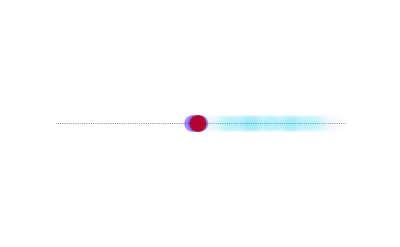

```mathematica
Show[
ListPlot[LatticeIrrational,Frame-> False,Axes-> False,PlotStyle-> {Black,PointSize[0.001]},PlotRange-> {{-10,Max[Flatten[LatticeIrrational]]+10},{-2,2}}],
Graphics[{Opacity[0.1],
PointSize[0.03],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]
}&/@dataLDoSPBCSorted,
BaseStyle-> 18
]

]
```